```mathematica
f[x_]=(1+Sqrt[3]*x/l)*Exp[-Sqrt[3]*x/l]
g[x_]=(1+Sqrt[5]*x/l+5*x^2/(3*l^2))*Exp[-Sqrt[5]*x/l]
```

ⅇ^(-(√3 x)/l) (1+(√3 x)/l)

ⅇ^(-(√5 x)/l) (1+(√5 x)/l+(5 x^2)/(3 l^2))

```mathematica
ff[x_]=D[f[x],x]//FullSimplify
gg[x_]=D[g[x],x]//FullSimplify
```

-(3 ⅇ^(-(√3 x)/l) x)/l^2

-(5 ⅇ^(-(√5 x)/l) x (l+√5 x))/(3 l^3)

```mathematica
fff[x_]=D[f[x],{x,2}]//FullSimplify
ggg[x_]=D[g[x],{x,2}]//FullSimplify
```

-(3 ⅇ^(-(√3 x)/l) (l-√3 x))/l^3

-(5 ⅇ^(-(√5 x)/l) (l^2+√5 l x-5 x^2))/(3 l^4)

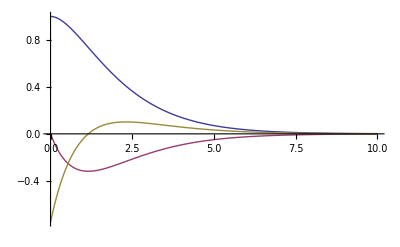

```mathematica
lo=2;
Plot[{f[x]/.l->lo,ff[x]/.l->lo,fff[x]/.l->lo},{x,0,10},PlotRange->Full]
```

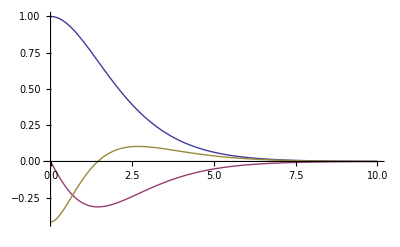

```mathematica
lo=2;
Plot[{g[x]/.l->lo,gg[x]/.l->lo,ggg[x]/.l->lo},{x,0,10},PlotRange->Full]
```

```mathematica
af[x_]=(1+Sqrt[3]*Abs[x]/l)*Exp[-Sqrt[3]*Abs[x]/l]
ag[x_]=(1+Sqrt[5]*Abs[x]/l+5*x^2/(3*l^2))*Exp[-Sqrt[5]*Abs[x]/l]
aff[x_]=-3/l^2*x*Exp[-Sqrt[3]*Abs[x]/l]
agg[x_]=-5/(3*l^2)*x*(1+Sqrt[5]/l*Abs[x])*Exp[-Sqrt[5]*Abs[x]/l]
afff[x_]=3/l^2*(Sqrt[3]/l*Abs[x]-1)*Exp[-Sqrt[3]*Abs[x]/l]
aggg[x_]=-5/(3*l^2)*(1+Sqrt[5]/l*Abs[x]+5/l^2*x^2)*Exp[-Sqrt[5]*Abs[x]/l]
```

ⅇ^(-(√3 Abs[x])/l) (1+(√3 Abs[x])/l)

ⅇ^(-(√5 Abs[x])/l) (1+(5 x^2)/(3 l^2)+(√5 Abs[x])/l)

-(3 ⅇ^(-(√3 Abs[x])/l) x)/l^2

-(5 ⅇ^(-(√5 Abs[x])/l) x (1+(√5 Abs[x])/l))/(3 l^2)

(3 ⅇ^(-(√3 Abs[x])/l) (-1+(√3 Abs[x])/l))/l^2

-(5 ⅇ^(-(√5 Abs[x])/l) (1+(5 x^2)/l^2+(√5 Abs[x])/l))/(3 l^2)

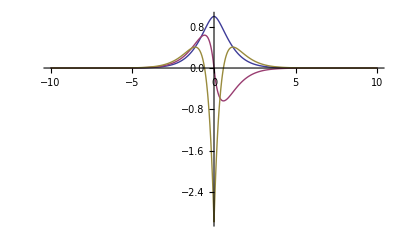

```mathematica
lo=1;
Plot[{af[x]/.l->lo,aff[x]/.l->lo,afff[x]/.l->lo},{x,-10,10},PlotRange->Full]
```

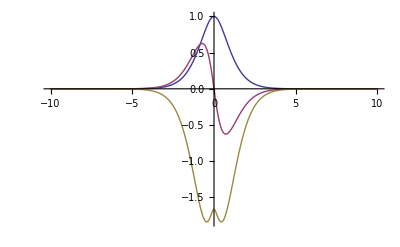

```mathematica
lo=1;
Plot[{ag[x]/.l->lo,agg[x]/.l->lo,aggg[x]/.l->lo},{x,-10,10},PlotRange->Full]
```

```mathematica
agg[x]
```

-(5 ⅇ^(-(√5 Abs[x])/l) x (1+(√5 Abs[x])/l))/(3 l^2)

```mathematica
agg[0]
agg[0.5]/.l->1
```

0

-0.577026

```mathematica
t[x_]=x^2
j[x_]=2x
```

x^2

2 x

```mathematica
ff[1]/.l->2
```

-3/4 ⅇ^(-(√3)/2)

```mathematica
%//N
```

-0.315465

```mathematica
(f[1]/.l->2)*(f[2]/.l->2)//N
```

0.379382

```mathematica
-3/4*Exp[-Sqrt[3]/2]*f[2]/.l->2*f[3]/.l->2 //N
```

-0.00365474

```mathematica
f1[x_]=f[x]/.l->2
```

ⅇ^(-(√3 x)/2) (1+(√3 x)/2)

```mathematica
f1 [1]*f1[2]*f1[3]
```

(1+(√3)/2) (1+√3) (1+(3 √3)/2) ⅇ^(-3 √3)

```mathematica
%//N
```

0.101582

```mathematica
f1[2]*f1[3]//N
```

0.129422

```mathematica
-3/4*Exp[-Sqrt[3]/2]//N
```

-0.315465

```mathematica
-3/4*Exp[-Sqrt[3]/2]*f1[2]*f1[3]
```

-3/4 (1+√3) (1+(3 √3)/2) ⅇ^(-3 √3)

```mathematica
%//N
```

-0.0408282

```mathematica
fd[x_]=-3/4*x*Exp[-Sqrt[3]/2*x]
```

-3/4 ⅇ^(-(√3 x)/2) x

```mathematica
fd[-1]*f1[2]*f1[3]//N
```

0.23077

```mathematica
fdd[x_]=fff[x]/.l->2
```

-3/8 ⅇ^(-(√3 x)/2) (2-√3 x)

```mathematica
fdd[3]*f1[1]*f1[2]//N
```

0.033838

```mathematica
fd[2]*fd[3]*f1[1]//N
```

0.0348763

```mathematica
g1[x_]=g[x]/.l->2
```

ⅇ^(-(√5 x)/2) (1+(√5 x)/2+(5 x^2)/12)

```mathematica
gd[x_]=gg[x]/.l->2
```

-5/24 ⅇ^(-(√5 x)/2) x (2+√5 x)

```mathematica
gdd[x_]=ggg[x]/.l->2
```

-5/48 ⅇ^(-(√5 x)/2) (4+2 √5 x-5 x^2)

```mathematica
gd[3]*g1[1]*g1[2]//N
```

-0.0825729

```mathematica
gd[1]//N
```

-0.288513

```mathematica
gd[0]
```

0